```mathematica
Needs["KiHA`","/Users/gangchen/Documents/GitHub/kinematicHopfAlgebra/KiHA.wl"]
```

KiHA(v5.7),Copyright 2022,author Gang Chen. It is licensed under the GNU General Public License v3.0. 
 KiHA is based on the work of Kinematic Hopf Algebra in CTP of Queen Mary University of London. It generates the duality all-n numerator for colour-kinematic duality and double copy in heavy mass effective 
 theory(HEFT), YM, YM-Scalar, YM-fermion, F3+F4 theory and DF2+YM theory. KiHA is built on some basic functions written by Gustav Mogull and Gregor Kaelin.
 use ?KiHA`* for help and a series of papers (2111.15649, 2208.05519, 2208.05886,2310.11943) for more reference.

```mathematica
Unprotect[p,F,ϵ,v,W];
declareVectorHead[{p,q,P,l,k,ϵ,v,w,a,at,b}]
declareTensorHead[{F,H,W,V,S},{"rank"-> 2}]
declareAntiTensorHead[{F,H,S}]
Protect[p,F,ϵ,v,W];
```

p declared as a 4-dimensional vector header.

q declared as a 4-dimensional vector header.

P declared as a 4-dimensional vector header.

l declared as a 4-dimensional vector header.

k declared as a 4-dimensional vector header.

ϵ declared as a 4-dimensional vector header.

v declared as a 4-dimensional vector header.

w declared as a 4-dimensional vector header.

a declared as a 4-dimensional vector header.

at declared as a 4-dimensional vector header.

b declared as a 4-dimensional vector header.

F declared as a 4-dimensional rank-2 tensor header.

H declared as a 4-dimensional rank-2 tensor header.

W declared as a 4-dimensional rank-2 tensor header.

V declared as a 4-dimensional rank-2 tensor header.

S declared as a 4-dimensional rank-2 tensor header.

## Useful subfunctions

```mathematica
ClearAll[FTtransfer]
FTtransfer[f_]:=Module[{logft,ftres},logft=((Series[f,{eps,0,1}]//Normal)//Cases[#,Times[gf__,Log[t]]:>Times[gf,Assuming[ω>0,Sqrt[2π]FourierTransform[  Log[Abs[t]],t,ω]//Simplify]]]&)[[1]];
ftres=logft/. {a_ t^od_:> (-I)^od D[a,{ω,od}], a_ t:> -I D[a,ω]}/.ω->1]
```

```mathematica
ClearAll[integralQ,notyt4Q,intD] (* This program is only for elliptic integral for particular Y*)
integralQ[f_]:= If[Head[f]===Inactive[Integrate],True,False]
notyt4Q[f_]:=If[Cases[f,y4,All]==={},True,False]
intD[f_integrate,yt4_,od_]:=intD[f,yt4,od]=Module[{intvar=f[[2,1]],ra=f[[2,2]],rb=f[[2,3]],int=f[[1]]},(Sum[Binomial[od,od1]D[D[int,{intvar,od-1-od1}],{yt4,od1}],{od1,0,od-1}])/.intvar->0/.yt4->0//Expand]
(*intD[a_notyt4Q f_,yt4_,od_]:=a intD[ f,yt4,od]*)
intD[a__ f_integrate,yt4_,od_]:=intD[a f,yt4,od]=Sum[Binomial[od,od1] D[Times[a],{yt4,od-od1}] intD[ f,yt4,od1],{od1,1,od}] /.yt4->0//Expand
intD[f_integrate,yt4_,0]:=0
intD[f_,yt4_,od_]:=D[f,{yt4,od}]/.yt4->0(* The od1=0 is not needed as for series expansion, it always vanish at yt4=0
*)
ClearAll[intSeries]
intSeries[f_,{var_,od_}]:=Sum[intD[f,var,odi] var^odi/(odi!)//FunctionExpand//Expand,{odi,0,od}]
intSeries[f_Plus,{var_,od_}]:=Sum[Sum[intD[f[[jj]],var,odi] var^odi/(odi!),{odi,0,od}],{jj,Length@f}]
```

```mathematica
ClearAll[Y2,Y4]
Y2[reps_]:=Y2[reps]=dot[a,a]/(-dot[b,b])/.reps
Y4[reps_]:=Y4[reps]=dot[a,b]/(-dot[b,b])/.reps
repat2a={at[1]->I a[1]};
repTsNew={T[f1_,repab_]:>T[f1/.y2->(Y2[repab])/.y4->(Y4[repab])/.dot[b,b]->(dot[b,b]/.repab)]};
```

```mathematica
numvaluesExact={dot[b[0],b[0]]->-1,dot[a[1],b[0]]->-1/5,y->12/10,ξ->1/2,dot[a[1],a[1]] ->-1/5,eps[a[1],b[0],v[1],v[2]]->√(-1+y^2) √(-dot[a[1],a[1]]-dot[a[1],b[0]]^2),C[2]->1,m[i_]:>1};
repeps=eps[a[1],b[0],v[1],v[2]]->√(-1+y^2) √(-dot[a[1],a[1]]-dot[a[1],b[0]]^2);
repepsat=eps[at[1],b[0],v[1],v[2]]->I √(-1+y^2) √(-dot[a[1],a[1]]-dot[a[1],b[0]]^2);
numvaluesFix={dot[b[0],b[0]]->-1,y->12/10,C[2]->1,ξ->1/2,m[i_]:>1};
```

```mathematica
EikonalClosedformList="data";
```

```mathematica
ellipticInt=EikonalClosedformList[[12]]//Cases[#,integrate[__],All]&//Union;
```

```mathematica
ef1=Integrate[1/(√(y2+2 y4-2 K[1]) √(y2+2 y4+(-2+K[1]) K[1])),K[1]];
ef2=Integrate[K[1]/(√(y2+2 y4-2 K[1]) √(y2+2 y4+(-2+K[1]) K[1])),K[1]];
```

```mathematica
repellipticIntegral={Rule[ellipticInt[[1]],(ef1/.K[1]->y4//Simplify)-(ef1/.K[1]->0//Simplify)],Rule[ellipticInt[[2]],(ef2/.K[1]->y4//Simplify)-(ef2/.K[1]->0//Simplify)]};
```

```mathematica
Monitor[numericCheck=Table[EikonalClosedformList[[ii]]/.repellipticIntegral/.repTsNew/.T[f_]:>f/.repat2a/.repeps/.numvaluesFix/.numvaluesVar/.{na->19/30,costheta->10/13}/.{σ[1]->1/2,σ[2]->2/3,σ[3]->3/4,σ[4]->4/5}//N,{ii,Length@EikonalClosedformList}];,ii]
```

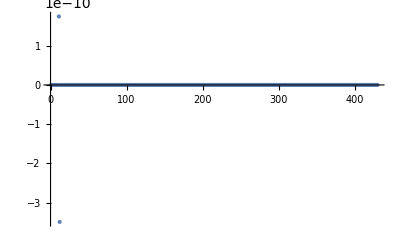

```mathematica
ListPlot[Im/@numericCheck,PlotRange->All]
```

```mathematica
(*Monitor[numresall=Table[ta=EikonalClosedformList[[jj]]/.Power[t,id_]:>FTtransfer[Power[t,id]]/eps/.repellipticIntegral/.repTsNew/.T[f_]:>f/.repat2a/.repeps/.numvaluesFix/.numvaluesVar/.{na->19/30,costheta->10/13};
NIntegrate[ta,{σ[1],0,1},{σ[2],0,1},{σ[3],0,1},{σ[4],0,1},WorkingPrecision->10],{jj,Length@EikonalClosedformList}];,jj]*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
(*NIntegrate[ta,{σ[1],0,1},{σ[2],0,1},{σ[3],0,1},{σ[4],0,1},WorkingPrecision->10]*)
```

0.3216134609

```mathematica
(*tb=EikonalClosedformList[[10]]/.Power[t,id_]:>FTtransfer[Power[t,id]]/eps/.repellipticIntegral/.repTsNew/.T[f_]:>f/.repat2a/.repeps/.numvaluesFix/.numvaluesVar/.{na->19/30,costheta->10/13};*)
```

```mathematica
(*NIntegrate[tb,{σ[1],0,1},{σ[2],0,1},{σ[3],0,1},{σ[4],0,1},WorkingPrecision->20]*)
```

$Aborted

## For spin expansion

```mathematica
intgrandY="data";
```

```mathematica
intgrandY[[9]]
```

-(3 ⅈ Cosh[dot[a[2],p[1]]] Cosh[dot[a[2],p[2]]] dot[p[1],v[1]] eps[a[1],p[1],p[2],v[1]] G[1,p[1]+p[2]] m[1]^2 m[2]^4)/(2 (-2+DD) dot[p[1],p[2]])

```mathematica
ellipticInt
```

{integrate[1/(√(y2+2 y4-2 K[1]) √(y2+2 y4+(-2+K[1]) K[1])),{K[1],0,y4}],integrate[K[1]/(√(y2+2 y4-2 K[1]) √(y2+2 y4+(-2+K[1]) K[1])),{K[1],0,y4}]}

```mathematica
repEK={EllipticE[f_]:>elip[2,f],EllipticK[f_]:>elip[1,f]};
repEKback={elip[2,f_]:>EllipticE[f],elip[1,f_]:>EllipticK[f]};
```

```mathematica
repelliptic={Rule[ellipticInt[[1]],intSeries[ellipticInt[[1]],{y4,10}]],Rule[ellipticInt[[2]],intSeries[ellipticInt[[2]],{y4,10}]]};
```

```mathematica
ClearAll[expandinys]
expandinys[f_]:=Module[{tc},tc= f/.repelliptic/.repEK//Collect[#,elip[__],Simplify]&;tc=(Series[tc/.repEKback,{y4,0,10},{y2,0,5}]//Normal)]
```

```mathematica
idd=9;
Length@EikonalClosedformList[[idd]]
Monitor[int2=Sum[EikonalClosedformList[[idd]][[jjj]]/.T[f1_,f2_]:>T[expandinys[f1],f2]/.repTsNew,{jjj,Length@EikonalClosedformList[[idd]]}];,jjj];
intMP1res=int2/.T[f_]:>f;
Length@intMP1res
Monitor[resNumz3=Sum[Series[intMP1res[[ii]]/.repat2a /.dot[b[0],b[0]]->-1/.a[1]->z a[1],{z,0,10}]//Normal,{ii,Length@intMP1res}];,ii];
resNumz3Sim=resNumz3//Collect[#,z,Simplify]&;
resexpand=Integrate[Integrate[Integrate[Integrate[resNumz3Sim,{σ[1],0,1}],{σ[2],0,1}],{σ[3],0,1}],{σ[4],0,1}]//Collect[#,z,Simplify]&;
```

8

```mathematica
forcompare={intgrandY[[9]],resexpand};
```

## Checking the incomplete elliptic integrals in I3

```mathematica
ellipticInt
```

{integrate[1/(√(y2+2 y4-2 K[1]) √(y2+2 y4+(-2+K[1]) K[1])),{K[1],0,y4}],integrate[K[1]/(√(y2+2 y4-2 K[1]) √(y2+2 y4+(-2+K[1]) K[1])),{K[1],0,y4}]}

```mathematica
ta=ellipticInt[[1]]//intSeries[#,{y4,36}]&;
ta/.y4->-2/10/.y2->-5/6//N[#,50]&
```

0.19761584050847514393182274788191169963315162414802

```mathematica
ellipticInt[[1]]/.repellipticIntegral/.y4->-2/10/.y2->-5/6//N[#,50]&
```

0.19761584050849003019680163460166772261549028135373

```mathematica
NIntegrate[1/(√(y2+2 y4-2 K[1]) √(y2+2 y4+(-2+K[1]) K[1]))/.y4->-2/10/.y2->-5/6,{K[1],0,-2/10}, WorkingPrecision->50]
```

0.19761584050849003019680163460166772261549028135373

```mathematica
ta=ellipticInt[[2]]//intSeries[#,{y4,36}]&;
```

```mathematica
ta/.y4->-2/10/.y2->-5/6//N[#,50]&
```

-0.021128746506134010040545837477768143121459128423558

```mathematica
ellipticInt[[2]]/.repellipticIntegral/.y4->-2/10/.y2->-5/6//N[#,50]&
```

-0.02112874650613383400629549602790203621217626898094+0. ⅈ

```mathematica
NIntegrate[K[1]/(√(y2+2 y4-2 K[1]) √(y2+2 y4+(-2+K[1]) K[1]))/.y4->-2/10/.y2->-5/6,{K[1],0,-2/10},Method->"LocalAdaptive", WorkingPrecision->50]
```

-0.02112874650613383400629549602790203621217626898094

## For finite spin effect

```mathematica
numvaluesVar={dot[a[1],b[0]]-> - na costheta,dot[a[1],a[1]]->-na^2};
```

```mathematica
idd=9;
intexample=EikonalClosedformList[[idd]]//Simplify;
```

```mathematica
Monitor[int2=Table[intexample[[jjj]]/.repellipticIntegral/.repTsNew,{jjj,Length@intexample}];,jjj];
```

```mathematica
int2num=int2/.T[f_]:>f/.repat2a/.numvaluesFix/.ξ ->3/5/.repeps/.y->12/10/.numvaluesVar//Total;
```

```mathematica
int2numNas=int2num/.{na->20/30,costheta->10/13};
```

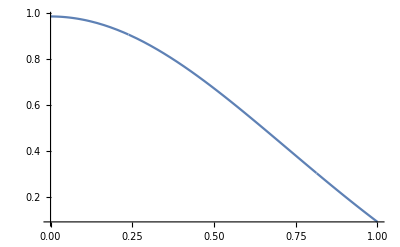

```mathematica
Plot[int2numNas,{σ[1],0,1},PlotRange->All]
```

```mathematica
resexpandNum=resexpand/.z->1/.repat2a/.numvaluesFix/.ξ ->3/5/.repeps/.y->12/10/.numvaluesVar;
```

```mathematica
Monitor[numresAll=Table[fnumall2=int2num/.{costheta->12/13,na->jj/30};
numres=NIntegrate[fnumall2,{σ[1],0,1},WorkingPrecision->20],{jj,1,20}];,{jj}]
```

```mathematica
Monitor[numresY=Table[resexpandNum/.{costheta->12/13,na->jj/30}//N,{jj,1,20}];,{ii,jj}]
```

```mathematica
numresFullRes=Table[T[jj/30.,numresAll[[jj]]],{jj,1,20}]//Flatten;
numresFullRes=numresFullRes/.T[f__]:>{f};
numExpandRes=Table[T[jj/30.,numresY[[jj]]],{jj,1,20}]//Flatten;
numExpandRes=numExpandRes/.T[f__]:>{f};
```

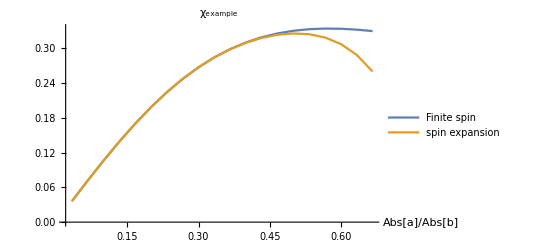

```mathematica
ListLinePlot[{numresFullRes,numExpandRes},AxesLabel->{Abs[a]/Abs[b]},PlotRange->Full,PlotLabel->"χ_example",PlotLegends->{"Finite spin","spin expansion"}]
```

## All expanded to a^8 order at y=2

```mathematica
(*EikonalExpandList="data";
Monitor[EikonalExpandList2=Table[EikonalExpandList[[ii]]//Collect[#,z,Simplify]&,{ii,Length@EikonalExpandList}];,ii]
EikonalExpandList2=EikonalExpandList2/.z->1;*)
```

```mathematica
(*List@@(EikonalCloseform/.T[f1_,f2_]:>T[f2]);
%/.a_ b_T:>b/;NumberQ[a]//FullSimplify//Union;
%//Length*)
```

```mathematica
EikonalExpandList2="data";
```

## Result for a background scalar scattering with a test Kerr black hole

```mathematica
numvaluesVar={dot[a[1],b[0]]-> - na costheta,dot[a[1],a[1]]->-na^2};
```

```mathematica
intScalarSpin="data";
```

```mathematica
intScalarSpinNum=intScalarSpin/.repat2a/.numvaluesFix/.repeps/.y->12/10/.numvaluesVar/.t[i_]:>σ[i];
```

```mathematica
intNum=intScalarSpinNum/.{costheta->2/10,na->3/20};
```

```mathematica
fresa=Total[intNum];
```

```mathematica
NIntegrate[fresa,{σ[1],0,1},{σ[2],0,1},WorkingPrecision->10]
```

23.80687221

## For compare

```mathematica
intgrandandResult="data";
```

```mathematica
integrand2IntegralNonY="data";
```